Joe Ingenito

Mathematica Day 1

1)

```mathematica
y[x_]:=c1*Exp[2x]*Sin[3x]+c2*Exp[2x]*Cos[3x]
```

2)

```mathematica
y[0]
```

c2

```mathematica
y[Pi]
```

-c2 ⅇ^(2 π)

3)

```mathematica
D[y[x],x]
```

3 c1 ⅇ^(2 x) Cos[3 x]+2 c2 ⅇ^(2 x) Cos[3 x]+2 c1 ⅇ^(2 x) Sin[3 x]-3 c2 ⅇ^(2 x) Sin[3 x]

```mathematica
y1[x_]:=3 c1 ⅇ^(2 x) Cos[3 x]+2 c2 ⅇ^(2 x) Cos[3 x]+2 c1 ⅇ^(2 x) Sin[3 x]-3 c2 ⅇ^(2 x) Sin[3 x]
```

4)

```mathematica
D[y1[x],x]
```

12 c1 ⅇ^(2 x) Cos[3 x]-5 c2 ⅇ^(2 x) Cos[3 x]-5 c1 ⅇ^(2 x) Sin[3 x]-12 c2 ⅇ^(2 x) Sin[3 x]

```mathematica
y2[x_]:=12 c1 ⅇ^(2 x) Cos[3 x]-5 c2 ⅇ^(2 x) Cos[3 x]-5 c1 ⅇ^(2 x) Sin[3 x]-12 c2 ⅇ^(2 x) Sin[3 x]
```

```mathematica
Expand[y2[x]-4*y1[x]+13*y[x]]
```

0

5)

```mathematica
Expand[y2[x]+4*y1[x]+13*y[x]]
```

24 c1 ⅇ^(2 x) Cos[3 x]+16 c2 ⅇ^(2 x) Cos[3 x]+16 c1 ⅇ^(2 x) Sin[3 x]-24 c2 ⅇ^(2 x) Sin[3 x]

6)

```mathematica
y[0]==3
```

c2==3

```mathematica
y1[x]
```

3 c1 ⅇ^(2 x) Cos[3 x]+2 c2 ⅇ^(2 x) Cos[3 x]+2 c1 ⅇ^(2 x) Sin[3 x]-3 c2 ⅇ^(2 x) Sin[3 x]

```mathematica
y1[0]==-2
```

3 c1+2 c2==-2

```mathematica
f[c1_]:=3 c1 + 6 + 2
```

```mathematica
Solve[f[c1]==0,c1]
```

{{c1→-8/3}}

7)

```mathematica
y[x]
```

c2 ⅇ^(2 x) Cos[3 x]+c1 ⅇ^(2 x) Sin[3 x]

```mathematica
g[x_]:=3*Exp[2x]*Cos[3x]-(8/3)*Exp[2x]*Sin[3x]
```

```mathematica
Plot[g,{-5,5,x}]
```

Plot::itraw: Raw object -5 cannot be used as an iterator.

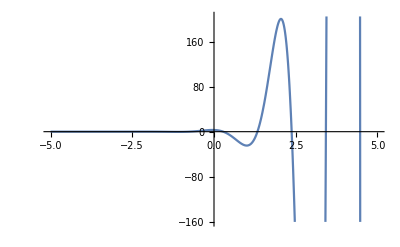

```mathematica
Plot[g[x],{x,-5,5}]
```

8)

```mathematica
z[x_]:=c1*x^(2/3)+c2*x^(-1)
```

9)

```mathematica
D[z[x],x]
```

-c2/x^2+(2 c1)/(3 x^(1/3))

```mathematica
z1[x_]:=-c2/x^2+(2 c1)/(3 x^(1/3))
```

```mathematica
D[z1[x],x]
```

(2 c2)/x^3-(2 c1)/(9 x^(4/3))

```mathematica
z2[x_]:=(2 c2)/x^3-(2 c1)/(9 x^(4/3))
```

```mathematica
a*(x^2)*z2[x]+4*x*z1[x]-2*z[x]
```

-2 (c2/x+c1 x^(2/3))+4 (-c2/x^2+(2 c1)/(3 x^(1/3))) x+a ((2 c2)/x^3-(2 c1)/(9 x^(4/3))) x^2

```mathematica
ff[x_]:=-2 (c2/x+c1 x^(2/3))+4 (-c2/x^2+(2 c1)/(3 x^(1/3))) x+a ((2 c2)/x^3-(2 c1)/(9 x^(4/3))) x^2
```

```mathematica
Solve[ff[x]==0,a]
```

{{a→3}}

General::ivar: 0 is not a valid variable.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.